```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"]];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
Print["Runs in the list: runNum = ",runNum={12695}]
Print["#Runs in the list: runn = ",runn=Dimensions[runNum][[1]]];
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
icycle=25;ChNum=4;binw=10;
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

Runs in the list: runNum = {12695}

#Runs in the list: runn = 1

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

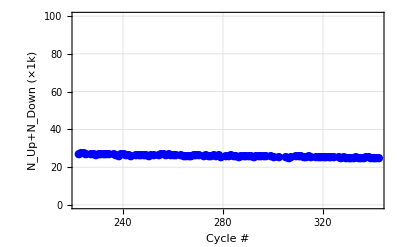
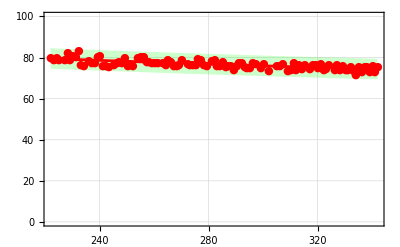

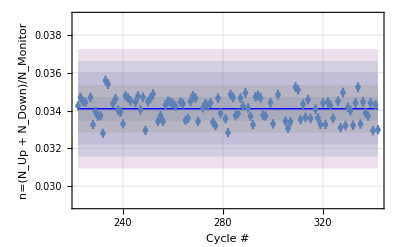

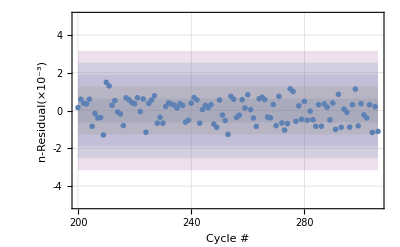

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.0340938 | 0.0000616622 | 552.913 | 3.42131×10^-182
bb | -6.11428×10^8 | 0. | -∞ | 0.
cc | 277205. | 0. | ∞ | 0.

{0.0000616622,0.,0.}

| DF | SS | MS
Model | 3 | 0.124376 | 0.0414586
Error | 104 | 0.0000423112 | 4.06838×10^-7
Uncorrected Total | 107 | 0.124418 | 
Corrected Total | 106 | 0.0000423112 |

```mathematica
runi=1;
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta5-2.dat"],metaStructure2];
begCy=200;
maxCy=Dimensions[data][[1]]-80;
ptud=Table[{data[[k]][[2]],{data[[k]][[27]]+data[[k]][[28]],Sqrt[data[[k]][[27]]+data[[k]][[28]]]}/1000},{k,begCy,maxCy}];
ptmon=Table[{data[[k]][[2]],{data[[k]][[30]],Sqrt[data[[k]][[30]]]}/10000},{k,begCy,maxCy}];
ptudmon=Table[{data[[k]][[2]],{(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]],((Sqrt[data[[k]][[27]]+data[[k]][[28]]])/data[[k]][[30]]+(Sqrt[data[[k]][[30]]]*(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]^2))}},{k,begCy,maxCy}];
ftud=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/1000},{k,begCy,maxCy}];
ftmon=Table[{data[[k]][[2]],(data[[k]][[30]])/10000},{k,begCy,maxCy}];
ftudmon=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]},{k,begCy,maxCy}];
nlmud=NonlinearModelFit[ftud,aa+bb Exp[-cc xx]+dd Exp[-ee xx],{{aa,1},{bb,10},{cc,.1},{dd,10},{ee,.1}},xx];
nlmmon=NonlinearModelFit[ftmon,aa+bb Exp[-cc xx]+dd Exp[-ee xx],{{aa,1},{bb,10},{cc,.1},{dd,10},{ee,.1}},xx];
nlmudmon=NonlinearModelFit[ftudmon,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
pt1=Show[{Plot[{nlmud[xx],nlmud[xx]+1,nlmud[xx]-1},{xx,data[[begCy]][[2]],data[[maxCy]][[2]]},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,100}},PlotStyle->{{Blue,Thickness[.005]},None,None},GridLines->Automatic,Frame->{True,True,False,False},Axes->None,FrameStyle->{{Blue,Thickness[.005]},
{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000}],
EDAListPlot[ptud,PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,100}},PlotStyle->{Blue},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
},ImagePadding->125];
pt2=Show[{
Plot[{nlmmon[xx],nlmmon[xx]+5,nlmmon[xx]-5},{xx,data[[begCy]][[2]],data[[maxCy]][[2]]},Filling->{2->{3}},FillingStyle->{Opacity[.5],Green},Axes->None,PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,100}},PlotStyle->{{Red,Thickness[.005]},None,None},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000}],
EDAListPlot[ptmon,PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,100}},PlotStyle->{Red},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
},ImagePadding->125];
pt3=Overlay[{pt1,pt2},ImageSize->1200]
sdftudmon=StandardDeviation[ftudmon[[;;,2]]];
avgftudmon=Mean[ftudmon[[;;,2]]];
pt4=Show[{
Plot[{
avgftudmon+sdftudmon,avgftudmon-sdftudmon,
avgftudmon+2sdftudmon,avgftudmon-2sdftudmon,
avgftudmon+3sdftudmon,avgftudmon-3sdftudmon,
avgftudmon+4sdftudmon,avgftudmon-4sdftudmon,
avgftudmon+5sdftudmon,avgftudmon-5sdftudmon,
nlmudmon[x]
},{x,data[[begCy]][[2]],data[[maxCy]][[2]]},Axes->None,Filling->{{1->{2}},{3->{4}},{5->{6}},{7->{8}},{9->{10}}},PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0.029,0.039}},PlotStyle->{None,None,None,None,None,None,None,None,None,None,{Blue,Thick}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n=(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[ptudmon,PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,0.04}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n=(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Red, Medium}]
},ImagePadding->150]
ptudmonres=Table[{k-1+begCy,1000nlmudmon["FitResiduals"][[k]]},{k,1,maxCy-begCy+1}];
sdptudmonres=StandardDeviation[ptudmonres[[;;,2]]];
avgptudmonres=Mean[ptudmonres[[;;,2]]];
pt5=Show[{
Plot[{sdptudmonres,-sdptudmonres,
2sdptudmonres,-2sdptudmonres,
3sdptudmonres,-3sdptudmonres,
4sdptudmonres,-4sdptudmonres,
5sdptudmonres,-5sdptudmonres
},{x,begCy,maxCy},Filling->{{1->{2}},{3->{4}},{5->{6}},{7->{8}},{9->{10}}},Axes->None,PlotRange->{{begCy,maxCy},{-5,5}},PlotStyle->{None,None},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n-Residual(×10^-3)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[ptudmonres,PlotRange->{{begCy,maxCy},{-.004,.004}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Red, Medium}]
},ImagePadding->150]
nlmudmon["ParameterTable"]
nlmudmon["ParameterErrors"]
nlmudmon["ANOVATable"]
```

-0.00148933

0.241326

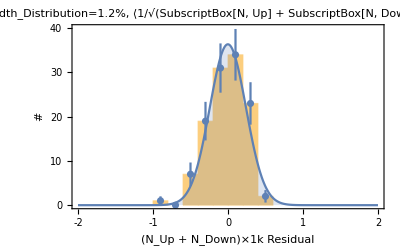

```mathematica
rmsptdatratio=Mean[nlmud["FitResiduals"]]
sdptdatratio=StandardDeviation[nlmud["FitResiduals"]]
errptsptres=Join[nlmud["FitResiduals"],Table[rmsptdatratio-.2,{k,1,10}]];
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Up + N_Down)×1k Residual","#"},Axes->False,PlotRange->{{-2,2},{0,40}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{32,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},PlotLabel->StringJoin["Width_Distribution=",ToString[SetPrecision[100*sdptdatratio/Total[Abs[nlmud["FitResiduals"]]],2]],"%, ⟨1/√(SubscriptBox[N, Up]  +  SubscriptBox[N, Down])⟩=",ToString[SetPrecision[100*Mean[ptud[[;;,2]][[;;,2]]/ptud[[;;,2]][[;;,1]]],2]],"%"]],
Plot[22PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,-2,2},Axes->False,PlotRange->{{-2,2},{0,40}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Up + N_Down)×1k Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-2,2},{0,40}}, Frame->True,FrameLabel->{"(N_Up + N_Down)×1k Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1000}]
}]
```

```mathematica
Join[{1,2,3},{4,5,6}]
```

{1,2,3,4,5,6}

0.00349021

1.47957

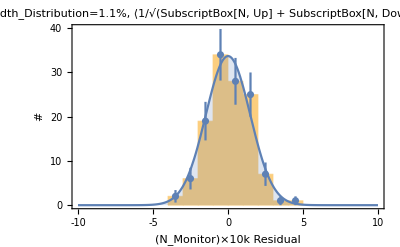

```mathematica
rmsptdatratio=Mean[nlmmon["FitResiduals"]]
sdptdatratio=StandardDeviation[nlmmon["FitResiduals"]]*1
errptsptres=Join[nlmmon["FitResiduals"],Table[rmsptdatratio+.5,{k,1,15}],Table[rmsptdatratio+3.5,{k,1,1}]];
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Monitor)×10k Residual","#"},Axes->False,PlotRange->{{-10,10},{0,40}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{32,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},PlotLabel->StringJoin["Width_Distribution=",ToString[SetPrecision[100*sdptdatratio/Total[Abs[nlmmon["FitResiduals"]]],2]],"%, ⟨1/√(SubscriptBox[N, Up]  +  SubscriptBox[N, Down])⟩=",ToString[SetPrecision[100*Mean[ptmon[[;;,2]][[;;,2]]/ptmon[[;;,2]][[;;,1]]],2]],"%"]],
Plot[125PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,-10,10},Axes->False,PlotRange->{{-10,10},{0,40}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Monitor)×10k Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-10,10},{0,40}}, Frame->True,FrameLabel->{"(N_Monitor)×10k Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1000}]
}]
```

-1.31644×10^-16

0.000423301

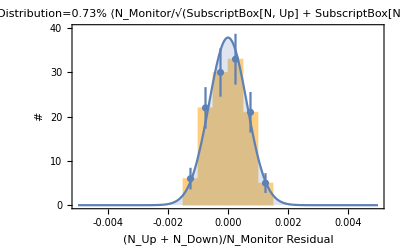

```mathematica
rmsptdatratio=Mean[nlmudmon["FitResiduals"]]
sdptdatratio=StandardDeviation[nlmudmon["FitResiduals"]]*.67
errptsptres=Join[nlmudmon["FitResiduals"],Table[rmsptdatratio-.00025,{k,1,10}]];
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},Axes->False,PlotRange->{{-.005,.005},{0,40}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},PlotLabel->StringJoin["Width_Distribution=",ToString[SetPrecision[100*sdptdatratio/Total[Abs[nlmudmon["FitResiduals"]]],2]],"%\n ⟨N_Monitor/√(SubscriptBox[N, Up]  +  SubscriptBox[N, Down])⟩=",ToString[SetPrecision[100*Mean[ptudmon[[;;,2]][[;;,2]]/ptudmon[[;;,2]][[;;,1]]],2]],"%"]],
Plot[0.06PDF[NormalDistribution[rmsptdatratio,sdptdatratio/.67],x],{x,-.005,.005},Axes->False,PlotRange->{{-.005,.005},{0,40}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-.005,.005},{0,40}}, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200}]
}]
```

```mathematica
rmsptdatratio=Mean[nlmudmon["FitResiduals"]]
sdptdatratio=StandardDeviation[nlmudmon["FitResiduals"]]*.67
errptsptres=Join[nlmudmon["FitResiduals"],Table[rmsptdatratio-.00025,{k,1,10}]];
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},Axes->False,PlotRange->{{-.005,.005},{0,40}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},PlotLabel->StringJoin["Width_Distribution=",ToString[SetPrecision[100*sdptdatratio/Total[Abs[nlmudmon["FitResiduals"]]],2]],"%\n ⟨N_Monitor/√(SubscriptBox[N, Up]  +  SubscriptBox[N, Down])⟩=",ToString[SetPrecision[100*Mean[ptudmon[[;;,2]][[;;,2]]/ptudmon[[;;,2]][[;;,1]]],2]],"%"]],
Plot[0.06PDF[NormalDistribution[rmsptdatratio,sdptdatratio/.67],x],{x,-.005,.005},Axes->False,PlotRange->{{-.005,.005},{0,40}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-.005,.005},{0,40}}, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200}]
}]
```

| Estimate | Standard Error | t-Statistic | P-Value
aa | 65.1165 | 268.279 | 0.24272 | 0.80871
bb | 239.162 | 260.699 | 0.917388 | 0.361104
cc | 0.00451749 | 0.239004 | 0.0189013 | 0.984957
dd | -207.982 | 260.695 | -0.797796 | 0.426842
ee | 0.00469695 | 0.281035 | 0.0167131 | 0.986698

| DF | SS | MS
Model | 5 | 631280. | 126256.
Error | 102 | 232.048 | 2.27498
Uncorrected Total | 107 | 631512. | 
Corrected Total | 106 | 475.272 |

{aa→65.1165,bb→239.162,cc→0.00451749,dd→-207.982,ee→0.00469695}

{268.279,260.699,0.239004,260.695,0.281035}

| Estimate | Standard Error | t-Statistic | P-Value
aa | 19.9608 | 55.8557 | 0.357363 | 0.721558
bb | 155.751 | 47.0019 | 3.31372 | 0.00127501
cc | 0.00414521 | 0.0518863 | 0.0798902 | 0.936481
dd | -143.816 | 47.0004 | -3.05989 | 0.00282943
ee | 0.00434865 | 0.0572056 | 0.076018 | 0.939554

| DF | SS | MS
Model | 5 | 73355.7 | 14671.1
Error | 102 | 6.1735 | 0.0605245
Uncorrected Total | 107 | 73361.9 | 
Corrected Total | 106 | 45.3919 |

0.0605245

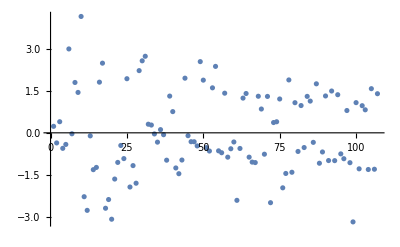

```mathematica
nlmmon["ParameterTable"]
nlmmon["ANOVATable"]
nlmmon["BestFitParameters"]
nlmmon["ParameterErrors"]
nlmud["ParameterTable"]
nlmud["ANOVATable"][[1]]
nlmud["ANOVATable"][[1]][[1]][[3]][[4]]
ListPlot[nlmmon["FitResiduals"]]
```

```mathematica
nlmud["MeanPredictionBands",ConfidenceLevel->.90][[1]]
nlmud["MeanPredictionBands",ConfidenceLevel->.90][[2]]
```

ⅇ^(-0.00849386 xx) (-143.816 ⅇ^(0.00414521 xx)+155.751 ⅇ^(0.00434865 xx)+ⅇ^(0.00849386 xx) (19.9608-1.65993 √(ⅇ^(-0.0339754 xx) (3119.86 ⅇ^(0.0339754 xx)+ⅇ^(0.0298302 xx) (-5241.88-902.033 xx)+ⅇ^(0.0296268 xx) (-5241.71+918.14 xx)+ⅇ^(0.0254816 xx) (4418.22-13.7702 xx-132.971 xx^2)+ⅇ^(0.025685 xx) (2209.18+759.553 xx+65.3081 xx^2)+ⅇ^(0.0252781 xx) (2209.03-773.273 xx+67.6848 xx^2)))))

ⅇ^(-0.00849386 xx) (-143.816 ⅇ^(0.00414521 xx)+155.751 ⅇ^(0.00434865 xx)+ⅇ^(0.00849386 xx) (19.9608+1.65993 √(ⅇ^(-0.0339754 xx) (3119.86 ⅇ^(0.0339754 xx)+ⅇ^(0.0298302 xx) (-5241.88-902.033 xx)+ⅇ^(0.0296268 xx) (-5241.71+918.14 xx)+ⅇ^(0.0254816 xx) (4418.22-13.7702 xx-132.971 xx^2)+ⅇ^(0.025685 xx) (2209.18+759.553 xx+65.3081 xx^2)+ⅇ^(0.0252781 xx) (2209.03-773.273 xx+67.6848 xx^2)))))

-1.44809×10^-16

0.000590867

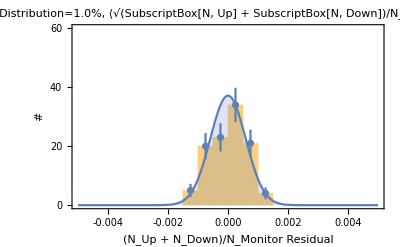

```mathematica
ptudmon2=Table[{data[[k]][[2]],{(data[[k]][[27]]+data[[k]][[28]])/(data[[k]][[27]]+data[[k]][[28]]+data[[k]][[30]]),((Sqrt[data[[k]][[27]]+data[[k]][[28]]])/data[[k]][[30]]+(Sqrt[data[[k]][[30]]]*(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]^2))}},{k,begCy,maxCy}];
ftudmon2=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/(data[[k]][[27]]+data[[k]][[28]]+data[[k]][[30]])},{k,begCy,maxCy}];
nlmudmon2=NonlinearModelFit[ftudmon2,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
rmsptdatratio=Mean[nlmudmon2["FitResiduals"]]
sdptdatratio=StandardDeviation[nlmudmon2["FitResiduals"]]
errptsptres=nlmudmon2["FitResiduals"];
Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},Axes->False,PlotRange->{{-.005,.005},{0,60}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{31,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},PlotLabel->StringJoin["Width_Distribution=",ToString[SetPrecision[100*sdptdatratio/Total[Abs[nlmudmon["FitResiduals"]]],2]],"%, ⟨√(SubscriptBox[N, Up]  +  SubscriptBox[N, Down])/N_Monitor⟩=",ToString[SetPrecision[100*Mean[ptudmon[[;;,2]][[;;,2]]/ptudmon[[;;,2]][[;;,1]]],2]],"%"]],
Plot[0.055PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,-.005,.005},Axes->False,PlotRange->{{-.005,.005},{0,60}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-.005,.005},{0,60}}, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1000}]
}]
```

## Extras: Appendix

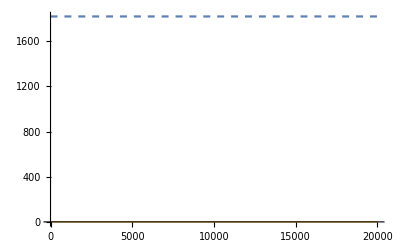

```mathematica
n1=10000;
n2=20000;
tau1=12;
tau2=880;
nud[ts_,nn_]:=nn NIntegrate[Exp[-t/tau1],{t,0,ts}]NIntegrate[Exp[-t/tau2],{t,0,180}];
nmon[ts_,nn_]:=nn NIntegrate[Exp[-t/tau1],{t,ts,ts+180}];
Plot[{nud[30,nn]/nmon[30,nn],nud[30,nn]/(nud[30,nn]+nmon[30,nn])},{nn,1,n2},PlotStyle->{Dashed,Thick}]
```